# Cartesian FDFD 1D wave solver discretization

He we discretize in Cartesian coordinates the 1D vector wave equation for plasmas. This is the simplest finite difference discretization you might think of. O(h^2) central difference, uniform grid h.

∇x∇xE - ω^2/c^2 * ϵ.E = iωμ_0J_A

```mathematica
ClearAll["Global`*"]

e0 =8.854187817 10^-12;
amu0=1.66053904 10^-27;
e=1.60217646 10^-19;
c=2.99792458 10^8;
me=9.10938188 10^-31;

LHS[E_,eps_]:=Simplify[(T1[E]+T2[E,eps])];
T1[E_]:=Simplify[Curl[Curl[E,{x,y,z}],{x,y,z}]];
T2[E_,eps_]:=-k0^2 Dot[eps,E];
eps={{exx,exy,exz},{eyx,eyy,eyz},{ezx,ezy,ezz}};
ExpVar=Exp[I(ky*y+kz*z)];
E1={Ex[x],Ey[x],Ez[x]}*ExpVar;
thisLHS=LHS[E1,eps]/ExpVar
CentralDiffRules={D[E_[x], x,x]->(Subscript[E, "i-1"]-2 Subscript[E, "i"]+Subscript[E, "i+1"])/(h^2),D[E_[x], x]->(-Subscript[E, "i-1"]+Subscript[E, "i+1"])/(2h),E_[x]->Subscript[E, "i"]};
CollectTerms={Subscript[Ex, "i-1"],Subscript[Ex, "i"],Subscript[Ex, "i+1"],Subscript[Ey, "i-1"],Subscript[Ey, "i"],Subscript[Ey, "i+1"],Subscript[Ez, "i-1"],Subscript[Ez, "i"],Subscript[Ez, "i+1"]};
CentralDiff=thisLHS/.CentralDiffRules;
Coeffs=Collect[CentralDiff,CollectTerms]
```

{(-exx k0^2+ky^2+kz^2) Ex[x]-exy k0^2 Ey[x]-exz k0^2 Ez[x]+ⅈ ky Ey'[x]+ⅈ kz Ez'[x],-eyx k0^2 Ex[x]-(eyy k0^2-kz^2) Ey[x]-eyz k0^2 Ez[x]-ky kz Ez[x]+ⅈ ky Ex'[x]-Ey''[x],-ezx k0^2 Ex[x]-(ezy k0^2+ky kz) Ey[x]-ezz k0^2 Ez[x]+ky^2 Ez[x]+ⅈ kz Ex'[x]-Ez''[x]}

{(-exx k0^2+ky^2+kz^2) Ex_i-exy k0^2 Ey_i-(ⅈ ky Ey_(i-1))/(2 h)+(ⅈ ky Ey_(i+1))/(2 h)-exz k0^2 Ez_i-(ⅈ kz Ez_(i-1))/(2 h)+(ⅈ kz Ez_(i+1))/(2 h),-eyx k0^2 Ex_i-(ⅈ ky Ex_(i-1))/(2 h)+(ⅈ ky Ex_(i+1))/(2 h)+(2/h^2-eyy k0^2+kz^2) Ey_i-(Ey_(i-1))/h^2-(Ey_(i+1))/h^2+(-eyz k0^2-ky kz) Ez_i,-ezx k0^2 Ex_i-(ⅈ kz Ex_(i-1))/(2 h)+(ⅈ kz Ex_(i+1))/(2 h)+(-ezy k0^2-ky kz) Ey_i+(2/h^2-ezz k0^2+ky^2) Ez_i-(Ez_(i-1))/h^2-(Ez_(i+1))/h^2}

Create an analytic solution and corresponding source term using the method of manufactured solutions (free-space) ...

0.27246

{ⅇ^(5 ⅈ π x),ⅇ^(5 ⅈ π x),0.01 ⅇ^(5 ⅈ π x)}

LHS[{ⅇ^(5 ⅈ π x),ⅇ^(5 ⅈ π x),0.01 ⅇ^(5 ⅈ π x)}]

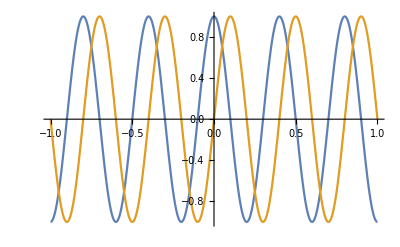

-Graphics-

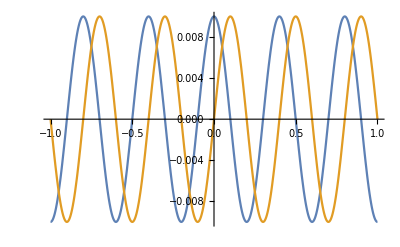

```mathematica
u={Ex,Ey, Ez }*Exp[I(kx x)];
exx=1;exy=0;exz=0;
eyx=0;eyy=1;eyz=0;
ezx=0;ezy=0;ezz=1;
xMax=1;xMin=-1;
nLambda=5;
lambda = (xMax-xMin)/nLambda;
kx = 2 Pi / lambda;
ky=0.1;
kz=0.05;
f=13 10^6;
w=2 Pi f;
k0=w/c
Ex = 1;Ey=1;Ez=0.01;
u
S=NumberForm[LHS[u],12]
Plot[{Re[u][[1]],Im[u][[1]]},{x,xMin,xMax}]
Plot[{Re[u][[2]],Im[u][[2]]},{x,xMin,xMax}]
Plot[{Re[u][[3]],Im[u][[3]]},{x,xMin,xMax}]
```

Setup the cold plasma dielectric

```mathematica
q[Z_]:=Z*e;
m[amu_]:=amu*amu0;
ϵ[Z_]:=q[Z]/Abs[q[Z]];
wc[Z_,B_,amu_]:=Abs[q[Z]]*B/m[amu];
wp[Z_,amu_,n_]:=Sqrt[n q[Z]^2/(m[amu] e0)];
K1[w_,Z_,amu_,n_,B_]:=1-wp[Z,amu,n]^2/(w^2-wc[Z,B,amu]^2);
K2[w_,Z_,amu_,n_,B_]:=(1/I) ϵ[Z] wc[Z,B,amu] wp[Z,amu,n]^2 / (w (w^2-wc[Z,B,amu]^2));
K3[w_,Z_,amu_,n_,B_]:=1-wp[Z,amu,n]^2/w^2;
epsilon[w_,Z_,amu_,n_,B_]:={{K1[w,Z,amu,n,B],K2[w,Z,amu,n,B],0},{-K2[w,Z,amu,n,B],K1[w,Z,amu,n,B],0},{0,0,K3[w,Z,amu,n,B]}};
sigma[epsilon_,w_]:=(epsilon-IdentityMatrix[3]) w e0 / I;

f=42 10^6;Z=1;amu=2; n=3.677 10^19; B=1.0;w=2 Pi f;

epsCold= epsilon[w,Z,amu,n,B];
sigCold = sigma[epsCold,w];
```

Solve the dispersion relation to estimate the kx

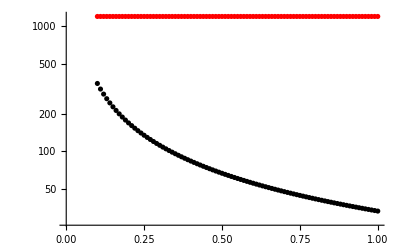

```mathematica
ExpVar0=Simplify[Exp[I(kx x)] ExpVar];
u0={Ex,Ey,Ez}ExpVar0;

f=13 10^6;Z={-1,1};amu={me/amu0,2}; n=4 10^19;w=2 Pi f;
k0=w/c;ky=0;kz=0;

Clear[B0,B];
thiseps=Sum[epsilon[w,Z[[s]],amu[[s]],n,B0],{s,1,Length[Z]}];
Coeffs0=CoefficientArrays[LHS[u0,thiseps]/ExpVar0,{Ex,Ey,Ez}];
disper=Table[{B0,Solve[Det[Normal[Coeffs0[[2]]]]==0,kx]},{B0,0.1,1.0,0.01}];
ax=disper[[All,1]];
kx1=disper[[All,2,1,1,2]];
kx1p=Table[{ax[[n]]+I ax[[n]],kx1[[n]]},{n,Length[ax]}];
kx2=disper[[All,2,2,1,2]];
kx2p=Table[{ax[[n]]+I ax[[n]],kx2[[n]]},{n,Length[ax]}];
kx3=disper[[All,2,3,1,2]];
kx3p=Table[{ax[[n]]+I ax[[n]],kx3[[n]]},{n,Length[ax]}];
kx4=disper[[All,2,4,1,2]];
kx4p=Table[{ax[[n]]+I ax[[n]],kx4[[n]]},{n,Length[ax]}];
ListLogPlot[{Re[kx1p],Im[kx1p],Re[kx2p],Im[kx2p],Re[kx3p],Im[kx3p],Re[kx4p],Im[kx4p]},PlotStyle->{Black,Red}]
```

Check above with Brambilla dispersion relation

Part::pkspec1: The expression s cannot be used as a part specification.

-1.75448×10^7

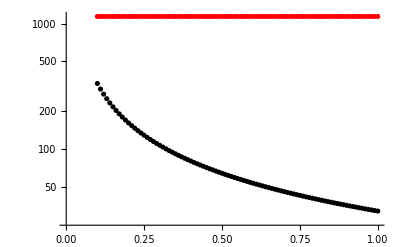

```mathematica
ClearAll["Global`*"]

e0 =8.854187817 10^-12;
amu0=1.66053904 10^-27;
e=1.60217646 10^-19;
c=2.99792458 10^8;
me=9.10938188 10^-31;

f=13 10^6;Z={-1,1};amu={me/amu0,2}; n=3.677 10^19; B=B0;w=2 Pi f;
k0=w/c;ky=0;kz=0;

w=2 Pi f;
q=e Z[[s]];
m = amu[[s]] amu0;
wp=Sqrt[n q^2/(m e0)];
wc=q B/m ;
SS=1-Sum[wp^2/(w^2-wc^2),{s,1,Length[Z]}];
PP=1-Sum[wp^2/w^2,{s,1,Length[Z]}];
LL=1-Sum[wp^2/w^2 w/(w-wc),{s,1,Length[Z]}];
RR=1-Sum[wp^2/w^2 w/(w+wc),{s,1,Length[Z]}];
nPar=kz c/w;

A1=SS;
B1=RR LL + PP SS -nPar^2(PP+SS);
C1=PP(nPar^2-RR)( nPar^2-LL);

kxAll=Table[{B0,Solve[A1 nPer^4-B1 nPer^2+C1==0,nPer][[All,1,2]] w/c},{B0,0.1,1.0,0.01}];
ax=kxAll[[All,1]];
kx1=kxAll[[All,2,1]];
kx2=kxAll[[All,2,2]];
kx3=kxAll[[All,2,3]];
kx4=kxAll[[All,2,4]];
kx1p=Table[{ax[[n]]+I ax[[n]],kx1[[n]]},{n,Length[ax]}];
kx2p=Table[{ax[[n]]+I ax[[n]],kx2[[n]]},{n,Length[ax]}];
kx3p=Table[{ax[[n]]+I ax[[n]],kx3[[n]]},{n,Length[ax]}];
kx4p=Table[{ax[[n]]+I ax[[n]],kx4[[n]]},{n,Length[ax]}];
ListLogPlot[{Re[kx1p],Im[kx1p],Re[kx2p],Im[kx2p],Re[kx3p],Im[kx3p],Re[kx4p],Im[kx4p]},PlotStyle->{Black,Red}]
```

Now construct a reasonable MMS analytic solution and source for testing ...

π

{ⅇ^(10 ⅈ x),ⅇ^(10 ⅈ x),0.01 ⅇ^(10 ⅈ x)}

{{4077.48,0.+6019.12 ⅈ,0},{0.-6019.12 ⅈ,4077.48,0},{0,0,-4810.05}}

{(-302.689-446.826 ⅈ) ⅇ^(10 ⅈ x),(-202.689+446.826 ⅈ) ⅇ^(10 ⅈ x),4.57071 ⅇ^(10 ⅈ x)}

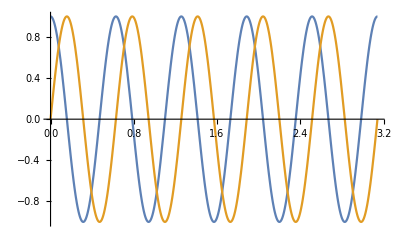

-Graphics-

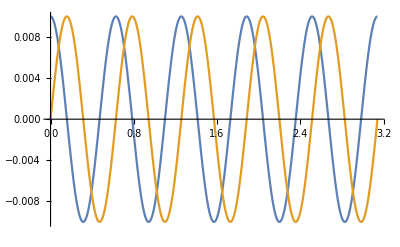

```mathematica
f=13 10^6;Z=1;amu=2; n=3.677 10^19; B=2.5;w=2 Pi f;
kx = 10;ky=0;kz=20;
Ex=1;Ey=1;Ez=0.01;
u2={Ex,Ey, Ez }*Exp[I(kx x)] ;
xMin=0;
nLambda=5;
lambda = (xMax-xMin)/nLambda;
xMax=nLambda * 2 Pi/kx
u2
thisEpsilon = epsilon[w,Z,amu,n,B]
S=LHS[u2,thisEpsilon]
Plot[{Re[u2][[1]],Im[u2][[1]]},{x,xMin,xMax}]
Plot[{Re[u2][[2]],Im[u2][[2]]},{x,xMin,xMax}]
Plot[{Re[u2][[3]],Im[u2][[3]]},{x,xMin,xMax}]
```